# Example damped oscillator

```mathematica
figuresDir=NotebookDirectory[]<>"example_damped_osc_figures/";
```

## Load package

```mathematica
SetDirectory[NotebookDirectory[]];
Needs["diffTVR`"]
```

```mathematica
?diffTVR`*
```

# Damped sin function, uniform noise

```mathematica
diff[x_,dx_]:=(RotateLeft[x]-x)[[;;-2]]/(dx)
```

```mathematica
integrate[pt1_,deriv_,dx_]:=Flatten[{pt1,pt1+(Accumulate[deriv]-0.5*(deriv+deriv[[1]]))*dx}];
```

```mathematica
err[true_,signal_]:=Module[
{ml,max,min,errval},
ml=Min[Length[signal],Length[true]];
max=Max[true[[;;ml]]];
min=Min[true[[;;ml]]];
errval=Mean[Abs[signal[[;;ml]]-true[[;;ml]]]/(max-min)];
errval=IntegerPart[(1000.0*errval)]/1000.0;
Style[Text[errval],FontSize->fontSize]
]
```

```mathematica
imgSize=500;
```

```mathematica
fontSize=20;
```

```mathematica
text[t_]:=Style[Text[t],FontSize->fontSize]
```

## Data

```mathematica
colors=(("DefaultPlotStyle"/. (Method/. Charting`ResolvePlotTheme["Scientific",ListLinePlot]))/. Directive[x_,__]:>x);
styleExactF=Darker[Green];
styleExact=Opacity[0.4,Darker[Green]];
styleNoisy=Directive[Opacity[0.7],colors[[1]]];
styleFiltered1=colors[[2]];
styleFiltered2=Darker[Magenta];
styleAve=Brown;
styleTVR=Black;
styleTVRFiltered=Gray;
styleFiltered1Filtered=Lighter[styleFiltered1];
styleFiltered2Filtered=Lighter[styleFiltered2];
styleNoisyFiltered=Blue;
```

```mathematica
rowLabels={
Null,
text["Signal"],
text["Deriv."],
text["Integrated"],
text["Deriv. \n error"],
text["Signal \n error"]
};
```

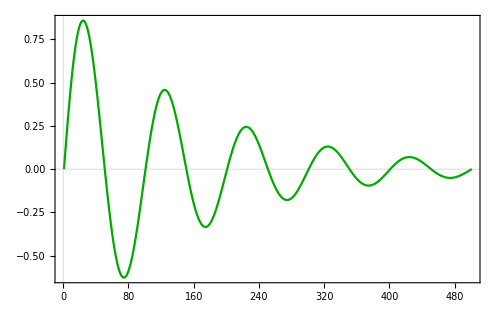
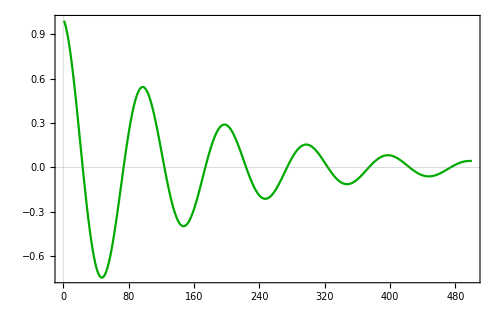
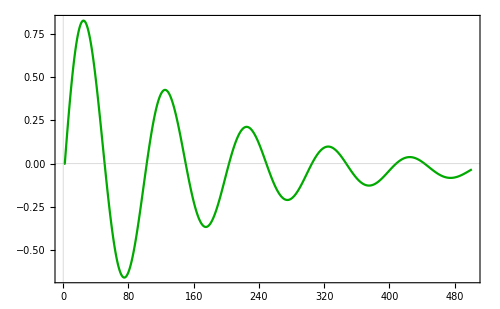
| Signal | Deriv. | Integrated | Deriv. 
 error | Signal 
 error
Exact signal 
 -> Diff. 
 -> Integrate | -Graphics- | -Graphics- | -Graphics- |  |

```mathematica
dx=10*Pi/500.0;
dataExact=Table[Sin[x]*Exp[-0.1*x],{x,0,10*Pi,dx}];
derivExact=diff[dataExact,dx];
rowExact={
text["Exact signal \n -> Diff. \n -> Integrate"],
ListLinePlot[dataExact,PlotStyle->styleExactF,ImageSize->imgSize],
ListLinePlot[derivExact,PlotStyle->styleExactF,ImageSize->imgSize],
ListLinePlot[integrate[dataExact[[1]],derivExact,dx],PlotStyle->styleExactF,ImageSize->imgSize]
};
pSignal=Grid[{rowLabels,rowExact}]
```

```mathematica
SetDirectory[figuresDir];
Export[figuresDir<>"signal.png",pSignal,ImageResolution->200]
```

/Users/oernst/software_public/tvm_differentiate/example_damped_osc_figures/signal.png

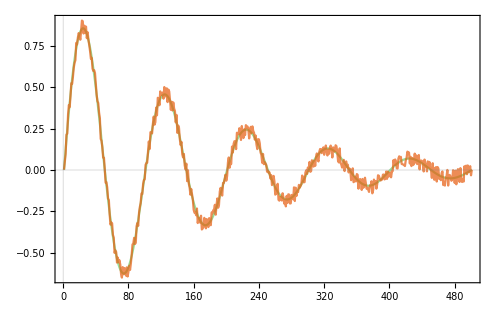
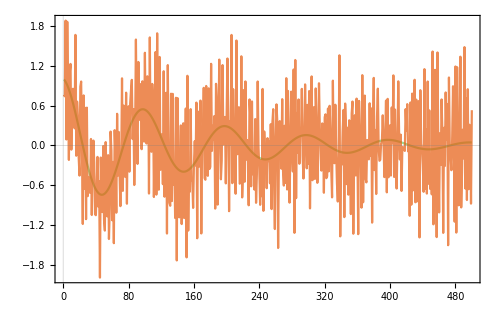
| Signal | Deriv. | Integrated | Deriv. 
 error | Signal 
 error
Noisy signal 
 -> Diff. 
 -> Integrate | -Graphics- | -Graphics- | -Graphics- |  |

```mathematica
dataNoisy=Table[x+0.05*RandomReal[{-1,1}],{x,dataExact}];
derivNoisy=diff[dataNoisy,dx];
rowNoisy={
text["Noisy signal \n -> Diff. \n -> Integrate"],
ListLinePlot[{dataExact,dataNoisy},PlotStyle->{styleExact,styleNoisy},ImageSize->imgSize],
ListLinePlot[{derivExact,derivNoisy},PlotStyle->{styleExact,styleNoisy},ImageSize->imgSize],
ListLinePlot[{dataExact,dataNoisy},PlotStyle->{styleExact,styleNoisy},ImageSize->imgSize]
};
pNoisy=Grid[{rowLabels,rowNoisy}]
```

```mathematica
SetDirectory[figuresDir];
Export[figuresDir<>"noisy.png",pNoisy,ImageResolution->200]
```

/Users/oernst/software_public/tvm_differentiate/example_damped_osc_figures/noisy.png

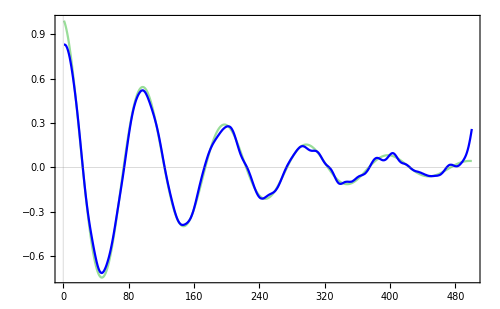
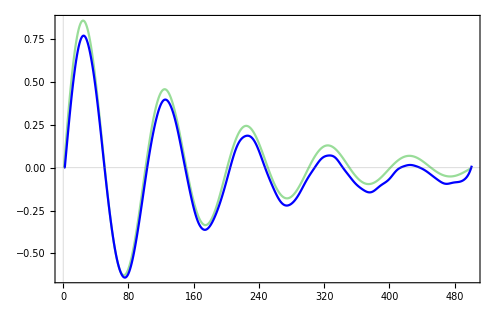
| Signal | Deriv. | Integrated | Deriv. 
 error | Signal 
 error
Signal 
 -> Diff. -> lowpass 
 -> Integrate | -Graphics- | -Graphics- | -Graphics- | 0.009 | 0.032

```mathematica
derivNoisyFiltered=LowpassFilter[derivNoisy,0.2];
rowNoisyFiltered={
text["Signal \n -> Diff. -> lowpass \n -> Integrate"],
ListLinePlot[{dataExact,dataNoisy},PlotStyle->{styleExact,styleNoisy},ImageSize->imgSize],
ListLinePlot[{derivExact,derivNoisyFiltered},PlotStyle->{styleExact,styleNoisyFiltered},PlotRange->All,ImageSize->imgSize],
ListLinePlot[{dataExact,integrate[dataNoisy[[1]],derivNoisyFiltered,dx]},PlotStyle->{styleExact,styleNoisyFiltered},ImageSize->imgSize],
err[derivExact,derivNoisyFiltered],
err[dataExact,integrate[dataNoisy[[1]],derivNoisyFiltered,dx]]
};
pFilteredDeriv=Grid[{rowLabels,rowNoisyFiltered}]
```

```mathematica
SetDirectory[figuresDir];
Export[figuresDir<>"filtered_deriv.png",pFilteredDeriv,ImageResolution->200]
```

/Users/oernst/software_public/tvm_differentiate/example_damped_osc_figures/filtered_deriv.png

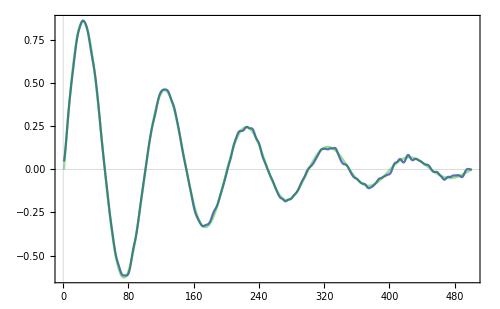
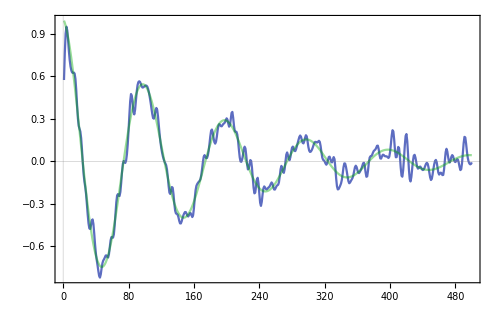
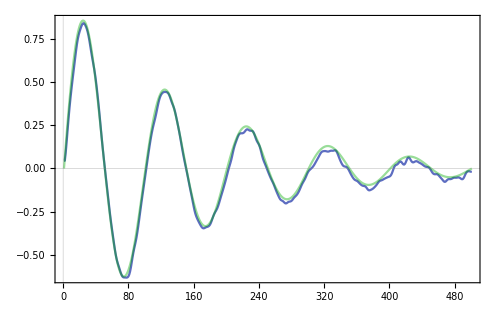
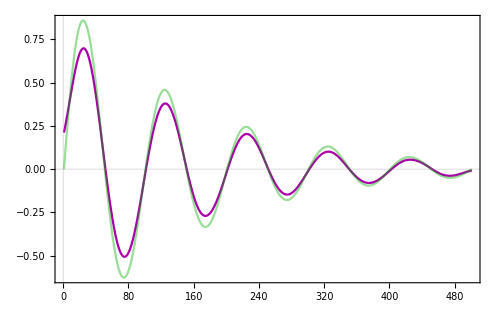
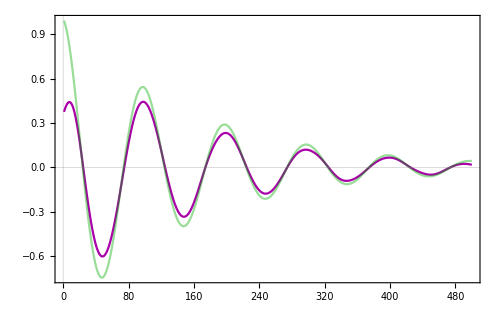
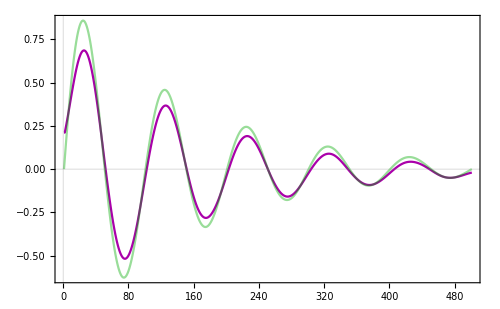
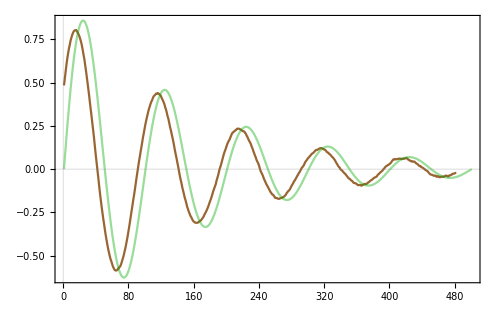
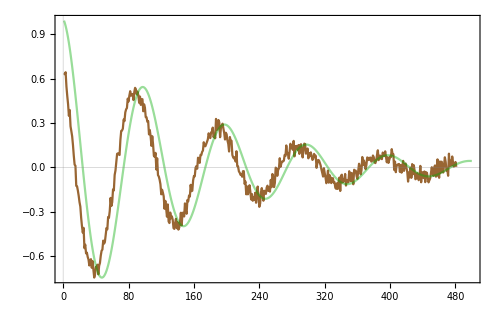
| Signal | Deriv. | Integrated | Deriv. 
 error | Signal 
 error
Signal -> lowpass 
 -> Diff. 
 -> Integrate | -Graphics- | -Graphics- | -Graphics- | 0.024 | 0.012
Signal -> lowpass 
 -> Diff. 
 -> Integrate | -Graphics- | -Graphics- | -Graphics- | 0.025 | 0.026
Signal -> moving ave. 
 -> Diff. 
 -> Integrate | -Graphics- | -Graphics- | -Graphics- | 0.068 | 0.071

```mathematica
dataFiltered1=LowpassFilter[dataNoisy,0.5];
dataFiltered2=LowpassFilter[dataNoisy,0.1];
dataAve=MovingAverage[dataNoisy,20];

derivFiltered1=diff[dataFiltered1,dx];
derivFiltered2=diff[dataFiltered2,dx];
derivAve=diff[dataAve,dx];

rowFiltered1={
text["Signal -> lowpass \n -> Diff. \n -> Integrate"],
ListLinePlot[{dataFiltered1,dataExact},PlotStyle->{styleFiltered1,styleExact},ImageSize->imgSize],
ListLinePlot[{derivFiltered1,derivExact},PlotStyle->{styleFiltered1,styleExact},ImageSize->imgSize],
ListLinePlot[{integrate[dataFiltered1[[1]],derivFiltered1,dx],dataExact},PlotStyle->{styleFiltered1,styleExact},ImageSize->imgSize],
err[derivExact,derivFiltered1],
err[dataExact,integrate[dataFiltered1[[1]],derivFiltered1,dx]]
};
rowFiltered2={
text["Signal -> lowpass \n -> Diff. \n -> Integrate"],
ListLinePlot[{dataFiltered2,dataExact},PlotStyle->{styleFiltered2,styleExact},ImageSize->imgSize],
ListLinePlot[{derivFiltered2,derivExact},PlotStyle->{styleFiltered2,styleExact},ImageSize->imgSize],
ListLinePlot[{integrate[dataFiltered2[[1]],derivFiltered2,dx],dataExact},PlotStyle->{styleFiltered2,styleExact},ImageSize->imgSize],
err[derivExact,derivFiltered2],
err[dataExact,integrate[dataFiltered2[[1]],derivFiltered2,dx]]
};
rowAve={
text["Signal -> moving ave. \n -> Diff. \n -> Integrate"],
ListLinePlot[{dataAve,dataExact},PlotStyle->{styleAve,styleExact},ImageSize->imgSize],
ListLinePlot[{derivAve,derivExact},PlotStyle->{styleAve,styleExact},ImageSize->imgSize],
ListLinePlot[{integrate[dataAve[[1]],derivAve,dx],dataExact},PlotStyle->{styleAve,styleExact},ImageSize->imgSize],
err[derivExact,derivAve],
err[dataExact,integrate[dataAve[[1]],derivAve,dx]]
};

pLowPass1=Grid[{rowLabels,rowFiltered1}];
pLowPass2=Grid[{rowLabels,rowFiltered2}];
pAve=Grid[{rowLabels,rowAve}];

Grid[{rowLabels,rowFiltered1,rowFiltered2,rowAve}]
```

```mathematica
SetDirectory[figuresDir];
Export[figuresDir<>"pLowPass1.png",pLowPass1,ImageResolution->200]
Export[figuresDir<>"pLowPass2.png",pLowPass2,ImageResolution->200]
Export[figuresDir<>"pAve.png",pAve,ImageResolution->200]
```

/Users/oernst/software_public/tvm_differentiate/example_damped_osc_figures/pLowPass1.png

/Users/oernst/software_public/tvm_differentiate/example_damped_osc_figures/pLowPass2.png

/Users/oernst/software_public/tvm_differentiate/example_damped_osc_figures/pAve.png

## Diff TVR

```mathematica
derivGuess=ConstantArray[0,Length[dataNoisy]+1];
noOptSteps=100;
alpha=0.01;
derivFinal=getDiffTVR[dataNoisy,derivGuess,noOptSteps,dx,alpha];
```

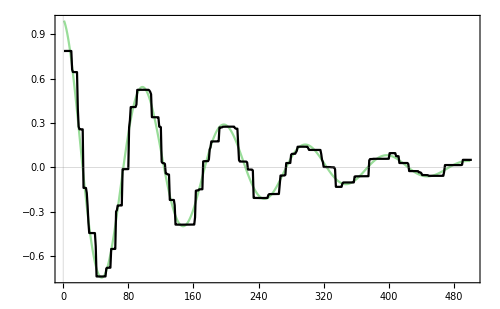
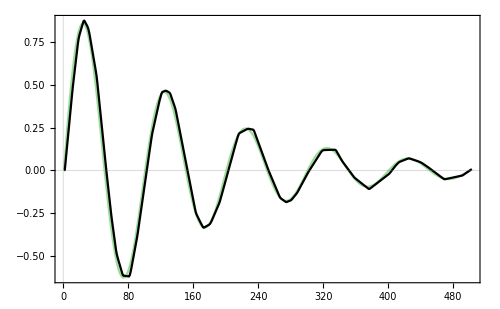
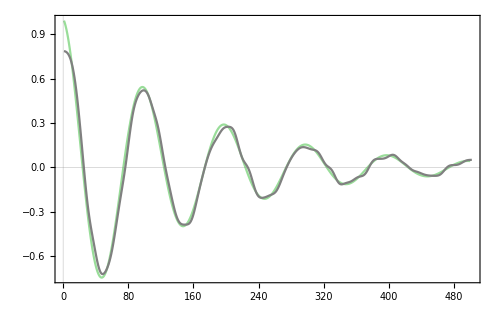
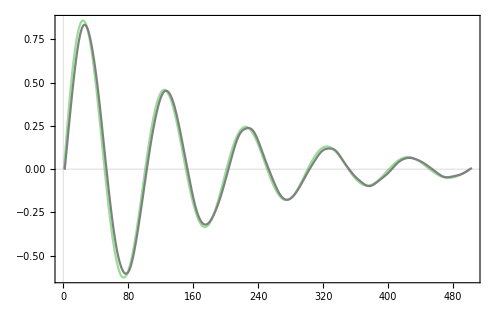
| Signal | Deriv. | Integrated | Deriv. 
 error | Signal 
 error
Signal 
 -> TVR diff. 
 -> Integrate | -Graphics- | -Graphics- | -Graphics- | 0.02 | 0.016
Signal 
 -> TVR diff. -> lowpass 
 -> Integrate | -Graphics- | -Graphics- | -Graphics- | 0.013 | 0.017

```mathematica
derivFinalFiltered=LowpassFilter[derivFinal,0.25];

rrowTVR={
text["Signal \n -> TVR diff. \n -> Integrate"],
ListLinePlot[{dataExact,dataNoisy},PlotStyle->{styleExact,styleNoisy},ImageSize->imgSize],
ListLinePlot[{derivExact,derivFinal},PlotStyle->{styleExact,styleTVR},PlotRange->All,ImageSize->imgSize],
ListLinePlot[{dataExact,integrate[dataNoisy[[1]],derivFinal,dx]},PlotStyle->{styleExact,styleTVR},PlotRange->All,ImageSize->imgSize],
err[derivExact,derivFinal],
err[dataExact,integrate[dataNoisy[[1]],derivFinal,dx]]
};
rrowTVRFiltered={
text["Signal \n -> TVR diff. -> lowpass \n -> Integrate"],
ListLinePlot[{dataExact,dataNoisy},PlotStyle->{styleExact,styleNoisy},ImageSize->imgSize],
ListLinePlot[{derivExact,derivFinalFiltered},PlotStyle->{styleExact,styleTVRFiltered},PlotRange->All,ImageSize->imgSize],
ListLinePlot[{dataExact,integrate[dataNoisy[[1]],derivFinalFiltered,dx]},PlotStyle->{styleExact,styleTVRFiltered},PlotRange->All,ImageSize->imgSize],
err[derivExact,derivFinalFiltered],
err[dataExact,integrate[dataNoisy[[1]],derivFinalFiltered,dx]]
};

Grid[{
rowLabels,
rrowTVR,
rrowTVRFiltered
}]
```

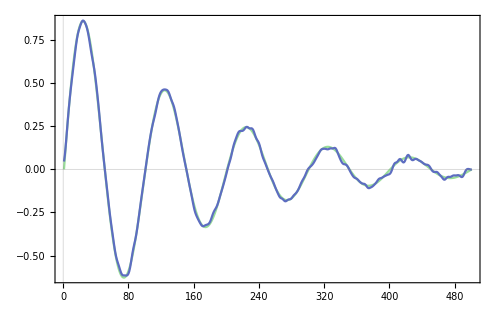
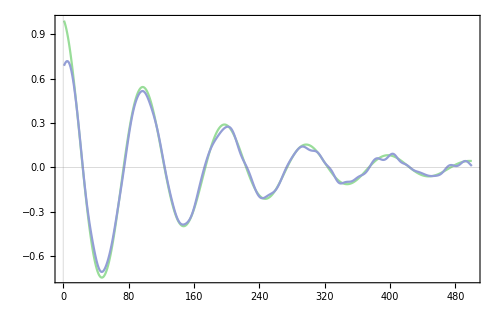
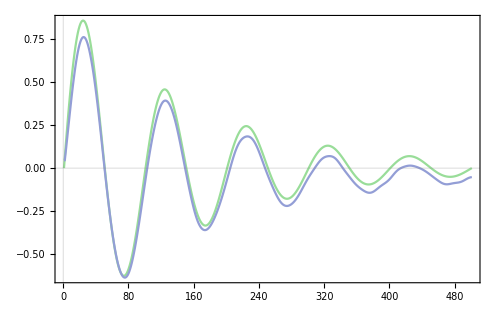
| Signal | Deriv. | Integrated | Deriv. 
 error | Signal 
 error
Signal -> lowpass 
 -> Diff. -> lowpass 
 -> Integrate | -Graphics- | -Graphics- | -Graphics- | 0.009 | 0.033

```mathematica
derivFiltered1Filtered=LowpassFilter[derivFiltered1,0.2];

rrowFiltered1Filtered={
text["Signal -> lowpass \n -> Diff. -> lowpass \n -> Integrate"],
ListLinePlot[{dataExact,dataFiltered1},PlotStyle->{styleExact,styleFiltered1},PlotRange->All,ImageSize->imgSize],
ListLinePlot[{derivExact,derivFiltered1Filtered},PlotStyle->{styleExact,styleFiltered1Filtered},PlotRange->All,ImageSize->imgSize],
ListLinePlot[{dataExact,integrate[dataFiltered1[[1]],derivFiltered1Filtered,dx]},PlotStyle->{styleExact,styleFiltered1Filtered},PlotRange->All,ImageSize->imgSize],
err[derivExact,derivFiltered1Filtered],
err[dataExact,integrate[dataFiltered1[[1]],derivFiltered1Filtered,dx]]
};

p=Grid[{
rowLabels,
rrowFiltered1Filtered
}]
```

```mathematica
SetDirectory[figuresDir];
Export["noisy_lp_diff_lp.png",p,ImageResolution->200]
```

noisy_lp_diff_lp.png

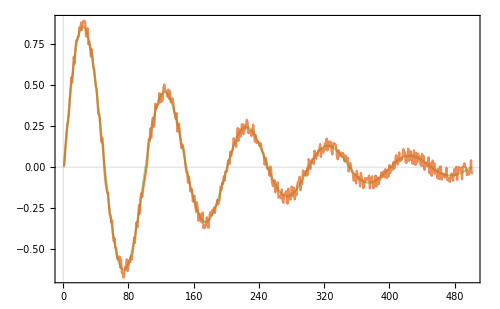
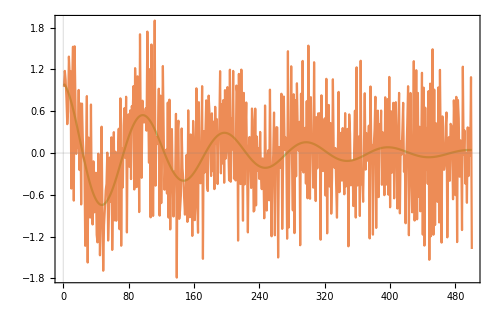
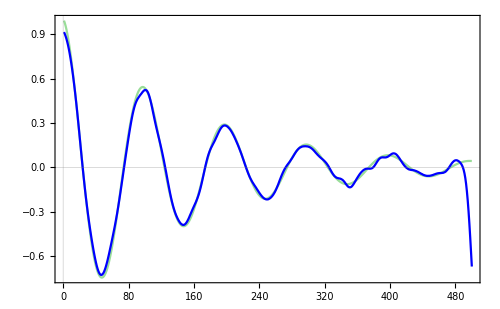
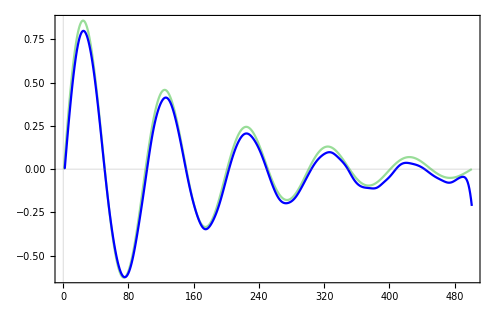
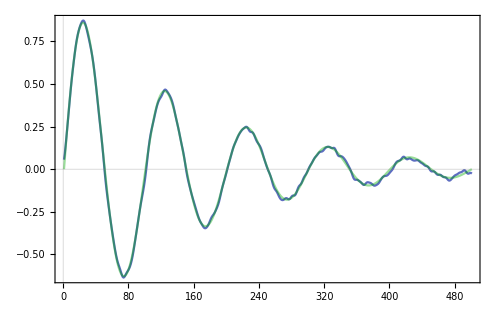
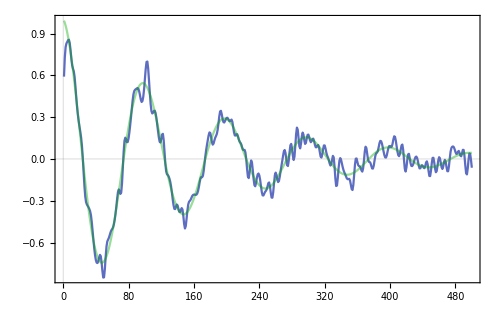
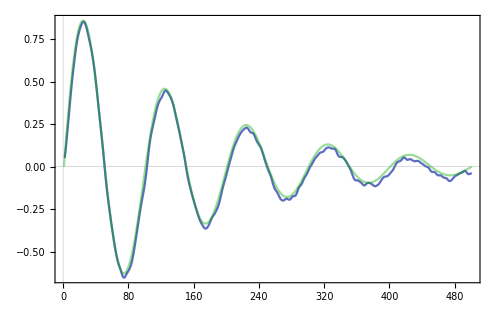
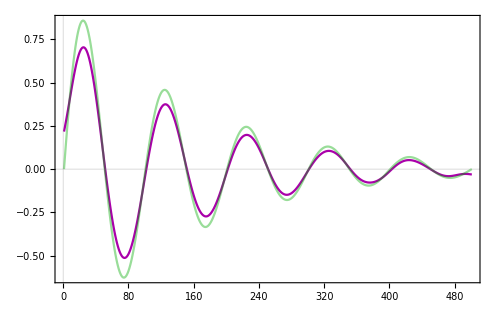
| Signal | Deriv. | Integrated | Deriv. 
 error | Signal 
 error
Exact signal 
 -> Diff. 
 -> Integrate | -Graphics- | -Graphics- | -Graphics- |  | 
Noisy signal 
 -> Diff. 
 -> Integrate | -Graphics- | -Graphics- | -Graphics- |  | 
Signal 
 -> Diff. -> lowpass 
 -> Integrate | -Graphics- | -Graphics- | -Graphics- | 0.011 | 0.02
Signal -> lowpass 
 -> Diff. 
 -> Integrate | -Graphics- | -Graphics- | -Graphics- | 0.024 | 0.013
Signal -> lowpass 
 -> Diff. 
 -> Integrate | -Graphics- | -Graphics- | -Graphics- | 0.025 | 0.026
Signal -> lowpass 
 -> Diff. -> lowpass 
 -> Integrate | -Graphics- | -Graphics- | -Graphics- | 0.01 | 0.03
Signal -> moving ave. 
 -> Diff. 
 -> Integrate | -Graphics- | -Graphics- | -Graphics- | 0.069 | 0.071
Signal 
 -> TVR diff. 
 -> Integrate | -Graphics- | -Graphics- | -Graphics- | 0.02 | 0.019
Signal 
 -> TVR diff. -> lowpass 
 -> Integrate | -Graphics- | -Graphics- | -Graphics- | 0.014 | 0.021

```mathematica
p=Grid[{
rowLabels,
rowExact,
rowNoisy,
rowNoisyFiltered,
rowFiltered1,
rowFiltered2,
rrowFiltered1Filtered,
rowAve,
rrowTVR,
rrowTVRFiltered
}]
```

```mathematica
SetDirectory[figuresDir];
Export["tog.png",p,ImageResolution->200]
```

tog.png